## Rectangle shape

Define a region:

```mathematica
regRectangle= Rectangle[{0,0},{2,1}];
```

Find all of its boundary edges:

```mathematica
edgesRectangle=MeshPrimitives[BoundaryDiscretizeRegion[regRectangle,MaxCellMeasure->{"Length"->0.01}],1];
(*boundaryEdges[regRectangle,MaxCellMeasure->.01]*)
```

From boundary edges, pick one randomly and one point within that:

```mathematica
edge1Rectangle=RandomChoice[edgesRectangle];
p1Rectangle=Mean@@edge1Rectangle;
```

From the initial point, pick a ray in a given direction:

```mathematica
Manipulate[Graphics[{{Opacity[.3],DiscretizeRegion@regRectangle},{Red,PointSize[Medium],Point[p1Rectangle]},{Green,Dynamic[ray1=HalfLine[p1Rectangle,pnt2-p1Rectangle]]}}],{{pnt2,Mean@@RandomChoice[edgesRectangle]},Locator}]
```

Given initial edge, point, and ray, find all 1,000 reflections within the region:

```mathematica
finalRectangle=NestList[reflect[#,edgesRectangle]&,{p1Rectangle,edge1Rectangle,ray1},200];//AbsoluteTiming
```

{38.244,Null}

Find all rays reflected within the region:

```mathematica
linesRectangle=Line/@Partition[finalRectangle[[All,1]],2,1];
```

Visualize them:

```mathematica
Manipulate[Graphics[{{edgesRectangle,Opacity[.2],LightBlue,DiscretizeRegion@regRectangle},{Red,Opacity[.2],linesRectangle[[;;s]]},{Blue,linesRectangle[[s]]}}],{s,1,Length[linesRectangle],1}]
```

## Circles

Define a region:

```mathematica
regCircles= RegionDifference[Disk[{0,0},2],Disk[{0,0},1]];
```

Find all of its boundary edges:

```mathematica
edgesCircles=MeshPrimitives[BoundaryDiscretizeRegion[regCircles,MaxCellMeasure->{"Length"->0.01}],1](*boundaryEdges[regCircles,MaxCellMeasure->.01]*);
```

From boundary edges, pick one randomly and one point within that:

```mathematica
edge1Circles=RandomChoice[edgesCircles];
p1Circles=Mean@@edge1Circles;
```

From the initial point, pick a ray in a given direction:

```mathematica
Manipulate[Graphics[{{Opacity[.3],DiscretizeRegion@regCircles},{Red,PointSize[Medium],Point[p1Circles]},{Green,Dynamic[ray1Circles=HalfLine[p1Circles,pnt2-p1Circles]]}}],{{pnt2,Mean@@RandomChoice[edgesCircles]},Locator}]
```

Given initial edge, point, and ray, find all 1,000 reflections within the region:

```mathematica
finalCircles=NestList[reflect[#,edgesCircles]&,{p1Circles,edge1Circles,ray1Circles},200];//AbsoluteTiming
```

{120.635,Null}

Find all rays reflected within the region:

```mathematica
linesCircles=Line/@Partition[finalCircles[[All,1]],2,1];
```

Visualize them:

```mathematica
Manipulate[Graphics[{{edgesCircles,Opacity[.2],LightBlue,DiscretizeRegion@regCircles},{Red,Opacity[.2],linesCircles[[;;s]]},{Blue,linesCircles[[s]]}}],{s,1,Length[linesCircles],1}]
```

## Rectangle with a circle hole

Define a region:

```mathematica
regHole= RegionDifference[Rectangle[{-2,-2},{2,2}],Disk[{0,0},1]];
```

Find all of its boundary edges:

```mathematica
edgesHole=MeshPrimitives[BoundaryDiscretizeRegion[regHole,MaxCellMeasure->{"Length"->0.01}],1](*boundaryEdges[regHole,MaxCellMeasure->.01]*);
```

From boundary edges, pick one randomly and one point within that:

```mathematica
edge1Hole=RandomChoice[edgesHole];
p1Hole=Mean@@edge1Hole;
```

From the initial point, pick a ray in a given direction:

```mathematica
Manipulate[Graphics[{{Opacity[.3],DiscretizeRegion@regHole},{Red,PointSize[Medium],Point[p1Hole]},{Green,Dynamic[ray1Hole=HalfLine[p1Hole,pnt2-p1Hole]]}}],{{pnt2,Mean@@RandomChoice[edgesHole]},Locator}]
```

Given initial edge, point, and ray, find all 1,000 reflections within the region:

```mathematica
finalHole=NestList[reflect[#,edgesHole]&,{p1Hole,edge1Hole,ray1Hole},200];//AbsoluteTiming
```

{170.549,Null}

Find all rays reflected within the region:

```mathematica
linesHole=Line/@Partition[finalHole[[All,1]],2,1];
```

Visualize them:

```mathematica
Manipulate[Graphics[{{edgesHole,Opacity[.2],LightBlue,DiscretizeRegion@regHole},{Red,Opacity[.2],linesHole[[;;s]]},{Blue,linesHole[[s]]}}],{s,1,Length[linesHole],1}]
```

## Stadium shape

Define a region:

```mathematica
regStadium= StadiumShape[];
```

Find all of its boundary edges:

```mathematica
edgesStadium=MeshPrimitives[BoundaryDiscretizeRegion[regStadium,MaxCellMeasure->{"Length"->0.01}],1](*boundaryEdges[regStadium,MaxCellMeasure->.01]*);
```

From boundary edges, pick one randomly and one point within that:

```mathematica
edge1Stadium=RandomChoice[edgesStadium];
p1Stadium=Mean@@edge1Stadium;
```

From the initial point, pick a ray in a given direction:

```mathematica
Manipulate[Graphics[{{Opacity[.3],DiscretizeRegion@regStadium},{Red,PointSize[Medium],Point[p1Stadium]},{Green,Dynamic[ray1Stadium=HalfLine[p1Stadium,pnt2-p1Stadium]]}}],{{pnt2,Mean@@RandomChoice[edgesStadium]},Locator}(*{{v,{-1,-1},"Direction of initial ray"},{-1,-1},{1,1}}*)]
```

DiscretizeRegion::regp: A correctly specified region expected at position 1 of DiscretizeRegion[regStadium].

Given initial edge, point, and ray, find all 1,000 reflections within the region:

```mathematica
finalStadium=NestList[reflect[#,edgesStadium]&,{p1Stadium,edge1Stadium,ray1Stadium},200];//AbsoluteTiming
```

{66.4465,Null}

Find all rays reflected within the region:

```mathematica
linesStadium=Line/@Partition[finalStadium[[All,1]],2,1];
```

Visualize them:

```mathematica
Manipulate[Graphics[{{edgesStadium,Opacity[.2],LightBlue,DiscretizeRegion@regStadium},{Red,Opacity[.2],linesStadium[[;;s]]},{Blue,linesStadium[[s]]}}],{s,1,Length[linesStadium],1}]
```

DiscretizeRegion::regp: A correctly specified region expected at position 1 of DiscretizeRegion[regStadium].

Part::take: Cannot take positions 1 through 160 in linesStadium.

Part::partd: Part specification linesStadium⟦160⟧ is longer than depth of object.

## Ellipse

### Exact boundary

```mathematica
ClearAll[a,b]
a=1;b=.5;
reg=Circle[{0,0},{a,b}];
```

```mathematica
ClearAll[tangent,crossing,next];
tangent[{px_,py_}]:=Reverse@{b^2 px,-a^2 py}
crossing[{x1_,y1_},{x2_,y2_}]:=Module[{a0=-(-y1+y2)/(x1-x2),b0=-(x2 y1-x1 y2)/(x1-x2)},{{x1,y1},SortBy[Quiet@SolveValues[{y==a0 x+b0,x^2/a^2+y^2/b^2==1},{x,y},Reals,WorkingPrecision->MachinePrecision],Norm[{x1,y1}-#]&][[-1]]}];
next[{p1_,p2_}]:=crossing[p2,ReflectionTransform[tangent[p2],p2][p1]]
```

```mathematica
{p1,p2}=RandomPoint[reg,2];
bounces=100;
data=NestList[next,{p1,p2},bounces];
collision=Partition[DeleteDuplicates@Flatten[data,1],3,1];
```

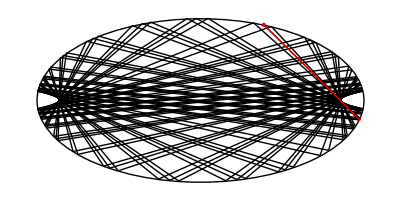

```mathematica
Graphics[{{reg},{Red,PointSize[Large],Point[{p1,p2}]},{Line/@data,Red,Line[{p1,p2}]}}]
```

### Discrete boundary

Define a region:

```mathematica
regEllipse= Disk[{0,0},{a,b}];
```

Find all of its boundary edges:

```mathematica
edgesEllipse=MeshPrimitives[BoundaryDiscretizeRegion[regEllipse,MaxCellMeasure->{"Length"->0.01}],1];
```

Get initial points of exact calculation

```mathematica
edge1Ellipse=SortBy[edgesEllipse,RegionDistance[#,p1]&][[1]];
p1Ellipse=Mean@@edge1Ellipse;
ray1Ellipse=HalfLine[p1Ellipse,p2-p1Ellipse];
```

Given initial edge, point, and ray, find all 1,000 reflections within the region:

```mathematica
finalEllipse=NestList[reflect[#,edgesEllipse]&,{p1Ellipse,edge1Ellipse,ray1Ellipse},100];//AbsoluteTiming
```

{19.7678,Null}

Find all rays reflected within the region:

```mathematica
linesEllipse=Line/@Partition[finalEllipse[[All,1]],2,1];
```

Visualize them:

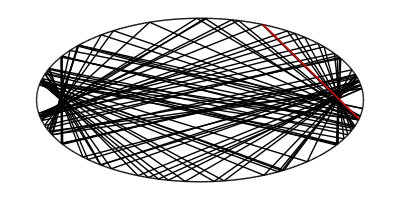

```mathematica
Graphics[{{edgesEllipse,linesEllipse},{Red,linesEllipse[[1]]}}]
```

### Poincare section

#### exact boundary

We should check if Poincare section is obtained correctly

```mathematica
θ=1/2(Module[{q1,p,q2},
{q1,p,q2}=#;Sign[Cross[Append[0][p-q1],Append[0][q2-p]][[-1]]]]PlanarAngle[#])&/@collision;
```

```mathematica
arcAngles=With[{θ=ArcTan[b/a(#[[1]])/(#[[2]])]},If[θ>0,θ,2π+θ]]&/@collision[[All,2]];
s=ArcLength[Circle[{0,0},{a,b},{0,#}]]&/@arcAngles;
```

```mathematica
ℒ=ArcLength[Circle[{0,0},{a,b},{0,2π}]]
```

4.84422

#### discrete boundary

```mathematica
θ2=1/2(Module[{q1,p,q2},
{q1,p,q2}=#;Sign[Cross[Append[0][p-q1],Append[0][q2-p]][[-1]]]]PlanarAngle[#])&/@Partition[finalEllipse[[All,1]],3,1];
```

```mathematica
arcAngles2=With[{θ=ArcTan[b/a(#[[1]])/(#[[2]])]},If[θ>0,θ,2π+θ]]&/@Partition[finalEllipse[[All,1]],3,1][[All,2]];
s2=ArcLength[Circle[{0,0},{a,b},{0,#}]]&/@arcAngles2;
```

#### Poincare section (also called phase space)

Depending on cell measure for BoundaryDiscretizeRegion, they are close enough (?)
does it mean when we have chaos such as Stadium, these errors are negligible?!

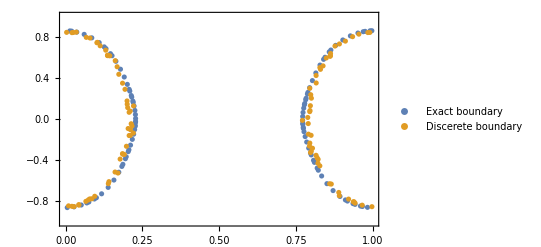

```mathematica
ListPlot[{Transpose[{s/ℒ,Sin[θ]}],Transpose[{s2/ℒ,Sin[θ2]}]},PlotRange->{{0,1},{-1,1}},Axes->False,Frame->True,PlotLegends->{"Exact boundary","Discerete boundary"}]
```

## new method (Sebastian)

```mathematica
ClearAll[reflect2];
reflect2[{p1_,edge1_,ray1_},boundaryedges_]:=Module[{boundaryLines,edge2,p2,reflectedP1,ray2},boundaryLines=Complement[boundaryedges,{edge1}];
(*Assuming an elipse,only 2 points intersect a line inside an elipse->Select First intersection*){edge2,{p2}}=DeleteCases[Flatten[#,2],{},3]&@Reap@SelectFirst[boundaryLines,!MatchQ[Sow[Graphics`Mesh`FindIntersections[{#,ray1}]],{}]&];
reflectedP1=ReflectionTransform[Subtract@@edge2[[1]],p2][p1];
ray2=HalfLine[p2,Subtract@@{reflectedP1,p2}];
{p2,edge2,ray2}]
```

## Initializations

Given a region, first discretizes a region reg into a MeshRegion. Then given its boundary edge indices, find all boundary edges, which will be a collection of lines

```mathematica
ClearAll[boundaryEdges];
boundaryEdges[reg_,opts:OptionsPattern[]]:=
Module[{dg,boundaryedgeindices},
dg=DiscretizeRegion[reg,FilterRules[{opts}, Options[DiscretizeRegion]]];
boundaryedgeindices=Flatten@Position[Length/@dg["ConnectivityMatrix"[1,2]]["AdjacencyLists"],1];MeshPrimitives[dg,{1,boundaryedgeindices}]]
```

Given an initial point, edge and ray, find the reflection inside a region with its given boundary edges. The result will be the next point on edges, its corresponding edge element and ray reflected from that point

```mathematica
ClearAll[reflect];
reflect[{p1_,edge1_,ray1_},boundaryedges_]:=Module[
{boundaryLines,edge2,p2,reflectedP1,ray2},
boundaryLines=Complement[boundaryedges,{edge1}];
{edge2,{p2}}=SortBy[DeleteCases[{#,Graphics`Mesh`FindIntersections[{#,ray1}]}&/@boundaryLines,{_,{}}],Abs[#[[-1,1]]-p1]&][[1]];
reflectedP1=ReflectionTransform[Subtract@@edge2[[1]],p2][p1];
ray2=HalfLine[p2,Subtract@@{reflectedP1,p2}];
{p2,edge2,ray2}
]
```